```mathematica
Needs["dsvsolve`"];
```

## Input

Edit or simply evaluate the following cell to see the input

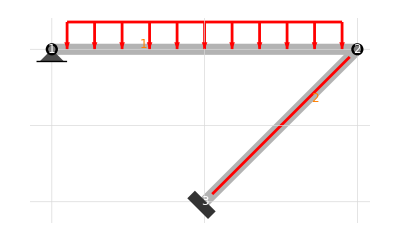

```mathematica
example={$$nodes->{{-2*L, L}, {2*L, L}, {0, -L}},
$$edges->{{1, 2}, {2, 3}},$$absname->s,
$$constraints->{{{"hinge", 1}}, {{"hinge", 1, 2}}, {{"clamp", 2}}},
$$bodyloads->{{1, {0, -q, 0}}},
$$nodalloads->{{1, {0, 0, 0}}},
$$predeformations->{{1, {0, 0, 0}}},
$$cdisplacements->{{1, {0, 0, 0}}},
$$EIoverEAL2->0};
(*All constraints are initialized to hinge constraints; use "BFConstraintsPalette[BFConstraintTypes];" to input different constraints.*)
BFShowInput[example]
```

## Output

Evaluate the following cell to solve the problem and see the output

```mathematica
BFClassify[example]; sol = {{Ns, Qs, Ms}, details} = BFForcesSolve[example];
(*A=Transpose[First[BFStaticProblem[example]]];MatrixForm[A]
BFShowRigidMotions[example]*)
(*BFEquations[example,"Nodal"]; sol = {{us, vs}, {Ns, Qs, Ms}, details} = BFDisplacementsSolve[example];*)
gsol=BFShowOutput[example, sol]
```

BFClassify::su: Statically undetermined system of order 1.
7 possible choices of static unknows are as follows:
1
N_1[0] | 2
N_1[1] | 3
N_2[0] | 4
Q_2[0] | 5
N_2[1] | 6
Q_2[1] | 7
M_2[1] |   |   |

BFClassify::kd: Kinematically determined system.

BFForcesSolve::suc: Chosen set of static unknows: {N_1[0]}

12345

Evaluate the following cell to print the above output

```mathematica
CellPrint/@Rest/@Last[sol];
Print/@Cases[gsol,Graphics[___],Infinity];
```

Dimensionless abscissa

s

Static equilibrium matrix

{{-1,0,0,1,0,0,0,0,0,0,0,0},{0,-1,0,0,1,0,0,0,0,0,0,0},{0,0,-1,0,4 L,1,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0,0,1,0,0},{0,0,0,0,0,0,0,-1,0,0,1,0},{0,0,0,0,0,0,0,0,-1,0,2 √2 L,1},{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,-2,0,0,-√2,√2,0,0,0,0},{0,0,0,0,-2,0,-√2,-√2,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,-1,0,0,0,0,0,0}}

Static equilibrium vector

{0,4 L q,8 L^2 q,0,0,0,0,0,0,0,0}

Fredholm condition: are the loads orthogonal to allowed rigid motions?

True

Bending stiffnesses

{EI,EI}

Axial stiffnesses

{∞,∞}

Degree of static undetermination

1

Some possible choices for the static unknowns

{{("N")_("1")[0]},{("N")_("1")[1]},{("N")_("2")[0]},{("Q")_("2")[0]},{("N")_("2")[1]},{("Q")_("2")[1]},{("M")_("2")[1]}}

Actually chosen static unknowns

{("N")_("1")[0]}

Reactions in the auxiliary problem 0

{{0,-2 L q,0,0,2 L q,0},{-√2 L q,-√2 L q,0,-√2 L q,-√2 L q,4 L^2 q}}

Reactions in the auxiliary problem 1

{{1,0,0,1,0,0},{-1/(√2),1/(√2),0,-1/(√2),1/(√2),-2 L}}

Internal actions (N,Q,M) in the auxiliary problem 0

{{0,-√2 L q},{2 L q (-1+2 s),-√2 L q},{-8 L^2 q (-1+s) s,4 L^2 q s}}

Internal actions (N,Q,M) in the auxiliary problem 1

{{1,-1/(√2)},{0,1/(√2)},{0,-2 L s}}

Mohr's Integrals: coefficient matrix ηij

{{(8 √2 L^3)/(3 EI)}}

Mohr's Integrals: vector ηi0

{-(16 √2 L^4 q)/(3 EI)}

Mohr's Integrals: solution for the static unknowns

{("N")_("1")[0]→2 L q}

Actual reactions

{{2 L q,-2 L q,0,2 L q,2 L q,0},{-2 √2 L q,0,0,-2 √2 L q,0,0}}

Actual internal actions (N,Q,M)

{{2 L q,-2 √2 L q},{2 L q (-1+2 s),0},{-8 L^2 q (-1+s) s,0}}

-Graphics-

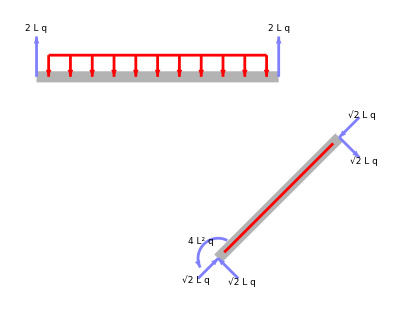

-Graphics-

-Graphics-

-Graphics-

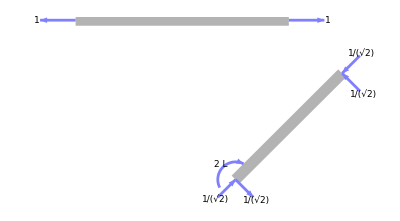

-Graphics-

-Graphics-

-Graphics-

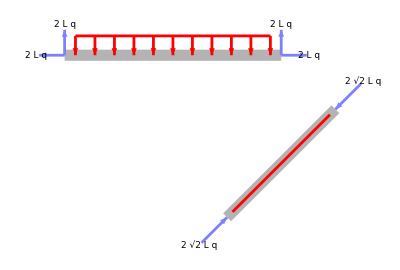

-Graphics-

-Graphics-

-Graphics-